```mathematica
(* Compare SPARC simple shock simulation with Taylor-Sedov theory *)
```

```mathematica
Δt=3.35*10^-15
```

3.35×10^-15

```mathematica
framePeriod=200000*Δt
```

6.7×10^-10

```mathematica
g=3.5/2.5
```

1.4

```mathematica
K=(75/(16*Pi))*((g-1)*(g+1)^2/(3*g-1))
```

1.0743

```mathematica
me=9.1094*10^-31
```

9.1094×10^-31

```mathematica
c=2.9979*10^8
```

2.9979×10^8

```mathematica
u0=.005*2.8*10^25*me*c^2
```

1.14618×10^10

```mathematica
radius=20.*10^-6
```

0.00002

```mathematica
ul=Integrate[u0*Exp[-x^2/radius^2]*2*Pi*x,{x,0,.0001}]
```

14.4033

```mathematica
nm=2.8*10^25*51078.5*me
```

1.30282

```mathematica
Rts[frame_]=(K*ul/nm)^0.25*Sqrt[frame*framePeriod]*10^6
```

48.0521 √frame

```mathematica
frames=Table[i,{i,0,200,1}];
```

```mathematica
Rtspts=Table[{frames[[i]],Rts[frames[[i]]]},{i,1,Length[frames]}];
```

```mathematica
R={{20,205},{50,327},{100,469},{200,665}}
```

{{20,205},{50,327},{100,469},{200,665}}

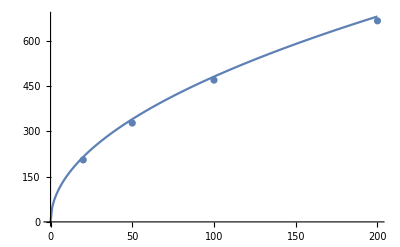

```mathematica
Show[ListPlot[R],ListPlot[Rtspts,Joined->True],PlotRange->All]
```